# Three Experiences Binarization and validation using ODE simulation of an oscillating artificial Model

```mathematica
SetDirectory@NotebookDirectory[];
```

```mathematica
<<Booned`
```

```mathematica
<<Bi4Back`
```

```mathematica
<<Functionsneededpackage`
```

```mathematica
Unprotect[t];Clear[t];Protect[t];
```

## RESEAU BOOLEEN EXEMPLE

```mathematica
FB={x1->x4&&x3,x2->x1,x3->!x2,x4->x2,x5->x3&&!x4}
```

{x1→x4&&x3,x2→x1,x3→!x2,x4→x2,x5→x3&&!x4}

```mathematica
StableFB=Association/@StableStates[FB]
```

{<|x1→False,x2→False,x3→True,x4→False,x5→True|>}

```mathematica
FindEquilibria@ModelOf[FB]
```

{{{x1→False,x2→False,x3→True,x4→False,x5→True}}}

## SIMULATION

```mathematica
name="oscillating  Model"
```

oscillating  Model

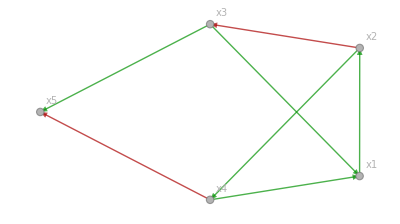

```mathematica
IG=NiceIG[InteractionGraphSimple[FB]]
```

### Parameters

Expression rate

```mathematica
κ=AssociationThread[Keys[FB],RandomReal[{1,5},Length[Keys[FB]]]]
```

<|x1→1.44221,x2→4.19657,x3→1.32307,x4→1.41236,x5→3.52675|>

```mathematica
κ=<|x1->4,x2->4,x3->1.5,x4->5,x5->3|>
```

<|x1→4,x2→4,x3→1.5,x4→5,x5→3|>

Degradation rate

```mathematica
γ=AssociationThread[Keys[FB],0.5]
```

<|x1→0.5,x2→0.5,x3→0.5,x4→0.5,x5→0.5|>

Threshold for being activated or inhibited.

```mathematica
θ=<|x1->0.5,x2->0.45,x3->0.45,x4->0.4,x5->0.6|> (*θ=Thresholding[Keys[FB],0.5,0.15] Threshold are generated randomly using the function Thresholding, see the fuction  in the package Functionsneeded*)
```

<|x1→0.5,x2→0.45,x3→0.45,x4→0.4,x5→0.6|>

```mathematica
Highlighted[TableForm[{Mean[θ],StandardDeviation[θ]}]]
```

0.48
0.0758288

### For a stable state

```mathematica
stablestate=StableFB[[1]]
```

<|x1→False,x2→False,x3→True,x4→False,x5→True|>

```mathematica
initialcondition=<|x1->4,x2->5,x3->7,x4->8,x5->4|>
```

<|x1→4,x2→5,x3→7,x4→8,x5→4|>

#### ODE

```mathematica
Framed@TableForm[
system=BooleanToODE[FB,t,κ,γ,θ, initialcondition,{hillm,hillp}]]
```

x1'[t]==4 hillp[x3[t],0.45] hillp[x4[t],0.4]-0.5 x1[t]
x1[0]==4
x2'[t]==4 hillp[x1[t],0.5]-0.5 x2[t]
x2[0]==5
x3'[t]==1.5 hillm[x2[t],0.45]-0.5 x3[t]
x3[0]==7
x4'[t]==5 hillp[x2[t],0.45]-0.5 x4[t]
x4[0]==8
x5'[t]==3 hillm[x4[t],0.4] hillp[x3[t],0.45]-0.5 x5[t]
x5[0]==4

```mathematica
fun=#[t]&/@Keys[FB];
```

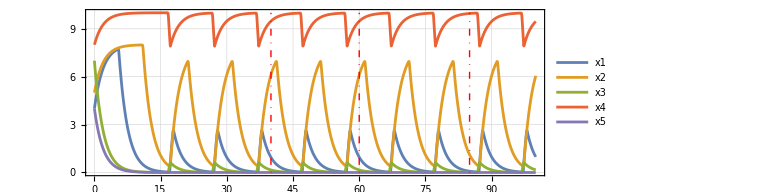

```mathematica
GG=Plot[Evaluate[fun/.NDSolve[system,Keys[FB],{t,0,100}]],{t,0,100}, PlotRange->All, PlotTheme->"Detailed",PlotStyle->Thick,PlotLegends->Placed[Keys[FB],Right],LabelStyle->Directive[FontFamily->"Franklin Gothic",11],
AspectRatio->1/3, PlotLabel->"", ImageSize->Large,Epilog-> {Thick,DotDashed, Red, Line[{{40,0},{40,10}}] ,Line[{{60,0},{60,10}}], Line[{{85,0},{85,10}}]}]
```

```mathematica
sol1=Evaluate[fun/.NDSolve[system,Keys[FB],{t,0,100}]]/.t->40
```

{{0.948409,6.11058,0.157608,9.47464,8.24461×10^-9}}

```mathematica
sol2=Evaluate[fun/.NDSolve[system,Keys[FB],{t,0,100}]]/.t->60
```

{{0.958369,6.09073,0.159263,9.46912,3.74305×10^-13}}

```mathematica
sol3=Evaluate[fun/.NDSolve[system,Keys[FB],{t,0,100}]]/.t->80
```

{{0.968433,6.07068,0.160936,9.46355,1.69934×10^-17}}

```mathematica
exp1=AssociationThread[Keys[FB],Flatten[sol1]]
```

<|x1→0.948409,x2→6.11058,x3→0.157608,x4→9.47464,x5→8.24461×10^-9|>

```mathematica
Boolprofileforexp1=Association@Table[exp1 ; var->exp1[var]> θ[var],{var,Keys[FB]}]
```

<|x1→True,x2→True,x3→False,x4→True,x5→False|>

```mathematica
exp2=AssociationThread[Keys[FB],Flatten[sol2]]
```

<|x1→0.958369,x2→6.09073,x3→0.159263,x4→9.46912,x5→3.74305×10^-13|>

```mathematica
Boolprofileforexp2=Association@Table[exp2 ; var->exp2[var]> θ[var],{var,Keys[FB]}]
```

<|x1→True,x2→True,x3→False,x4→True,x5→False|>

```mathematica
exp3=AssociationThread[Keys[FB],Flatten[sol3]]
```

<|x1→0.968433,x2→6.07068,x3→0.160936,x4→9.46355,x5→1.69934×10^-17|>

```mathematica
Boolprofileforexp3=Association@Table[exp3 ; var->exp3[var]> θ[var],{var,Keys[FB]}]
```

<|x1→True,x2→True,x3→False,x4→True,x5→False|>

# The Boolean profiles using our proposed Binarization method

```mathematica
Biomarker=<||>;
```

```mathematica
B=Bi4Back[IG,exp1,Biomarker, 0.2, 0.05]
```

<|x4→True,x5→False,x2→True,x3→False,x1→True|>

```mathematica
Bi4Back[IG,exp2,Biomarker, 0.2, 0.05]
```

<|x4→True,x5→False,x2→True,x3→False,x1→True|>

```mathematica
Bi4Back[IG,exp3,Biomarker, 0.2, 0.05]
```

<|x4→True,x5→False,x2→True,x3→False,x1→True|>

```mathematica
Distanceofdissimilarity[{Bi4Back[IG,exp1,Biomarker, 0.2, 0.05]}  ,Boolprofileforexp1]
```

{0}

```mathematica
Distanceofdissimilarity[{Bi4Back[IG,exp2,Biomarker, 0.2, 0.05]}  ,Boolprofileforexp2]
```

{0}

```mathematica
Distanceofdissimilarity[{Bi4Back[IG,exp3,Biomarker, 0.2, 0.05]}  ,Boolprofileforexp3]
```

{0}